```mathematica
vfrule = {vf->3/2};

Inverse[ⅈ ω PauliMatrix[0]-vf kx PauliMatrix[1]-vf ky PauliMatrix[2]]
```

{{(ⅈ ω)/(-kx^2 vf^2-ky^2 vf^2-ω^2),(kx vf-ⅈ ky vf)/(-kx^2 vf^2-ky^2 vf^2-ω^2)},{(kx vf+ⅈ ky vf)/(-kx^2 vf^2-ky^2 vf^2-ω^2),(ⅈ ω)/(-kx^2 vf^2-ky^2 vf^2-ω^2)}}

```mathematica
Integrate[{{(ⅈ ω)/(-kx^2 vf^2-ky^2 vf^2-ω^2),(kx vf)/(-kx^2 vf^2-ky^2 vf^2-ω^2)},{(kx vf)/(-kx^2 vf^2-ky^2 vf^2-ω^2),(ⅈ ω)/(-kx^2 vf^2-ky^2 vf^2-ω^2)}},{ky,-∞,∞},GenerateConditions->False]
```

{{-(ⅈ π ω √(vf^2/(kx^2 vf^2+ω^2)))/vf^2,-(kx π √(vf^2/(kx^2 vf^2+ω^2)))/vf},{-(kx π √(vf^2/(kx^2 vf^2+ω^2)))/vf,-(ⅈ π ω √(vf^2/(kx^2 vf^2+ω^2)))/vf^2}}

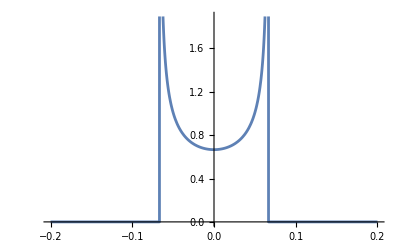

```mathematica
Plot[Im[(ω √(vf^2/(kx^2 vf^2-ω^2)))/vf^2]/.{vf->3/2,ω->0.1},{kx,-0.2,0.2}]
```

```mathematica
G [z_, kx_,ky_, vf_] := Inverse[z PauliMatrix[0]+vf ky PauliMatrix[1]+vf kx PauliMatrix[2]]
G[ω + I η, kx,ky,vf][[1,1]]
```

(ⅈ η+ω)/(-kx^2 vf^2-ky^2 vf^2-η^2+2 ⅈ η ω+ω^2)

```mathematica
resfastrec = Integrate[1/(2Pi)G[ω+I η, kx, ky, vf] [[1,1]], {ky, -Infinity,Infinity},GenerateConditions->False]
```

-(√(vf^2/(kx^2 vf^2+(η-ⅈ ω)^2)) (ⅈ η+ω))/(2 vf^2)

```mathematica
Limit[resfastrec,η->0, Direction->"FromAbove"]
```

-(ω √(vf^2/(kx^2 vf^2-ω^2)))/(2 vf^2)

```mathematica
Manipulate[Plot[-Im@resfastrec/.vfrule/.{ω-> 0.0002}/.η->10^-i, {kx,-0.001,0.001}, PlotRange->Full],{i,0,8,1}]
```

```mathematica
Simplify[Integrate[-Im[resfastrec], {kx,-1,1}],Assumptions->{η>0, ω>0, vf>0}]
```

∫_-1^1 1/2 Im[(√(1/(kx^2 vf^2+(η-ⅈ ω)^2)) (ⅈ η+ω))/vf]ⅆkx

```mathematica
Manipulate[Plot[1/(a Pi)1/(1+x^2/a^2),{x,-5,5},PlotRange->Full],{a,0.00001,2}]
```

```mathematica
FullSimplify[Integrate[1/(a Pi)1/(1+x^2/a^2),{x,-Infinity,Infinity},GenerateConditions->False],Assumptions->a>0]
```

1

```mathematica
NIntegrate[1/(a Pi)1/(1+(x-0.21231)^2/a^2)/.{a-> 10^-7},{x,0,1},MaxRecursion->10000,WorkingPrecision->12,AccuracyGoal->12,PrecisionGoal->12]
```

0.999999809663

```mathematica
Integrate[Sin[Pi x],{x,0,1}]
```

2/π